```mathematica
(* Finger throw *)
Clear[x,y,a,b,c,d,e,f,gamma];
X = Solve[{x == a+b*x+c*y,y==d+e*x+f*y},{x,y}];
X

Clear[Vs1,Vs2,V,a,R,L,gamma];
V =Solve[{Vs1 == a*(R+gamma*Vs1)+(1-a)*gamma*Vs2, Vs2 == a*gamma*Vs1+(1-a)*(L+gamma*Vs2)},{Vs1,Vs2}];
FullSimplify[V]
```

{{x→-(a+c d-a f)/(-1+b+c e+f-b f),y→-(d-b d+a e)/(-1+b+c e+f-b f)}}

{{Vs1→-(a R+(-1+a) gamma ((-1+a) L+a R))/(-1+gamma),Vs2→-((-1+a) (-1+a gamma) L+a^2 gamma R)/(-1+gamma)}}

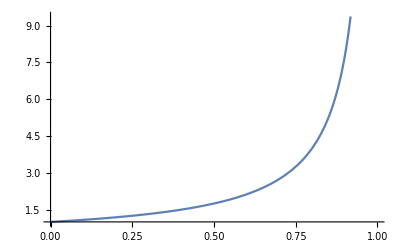

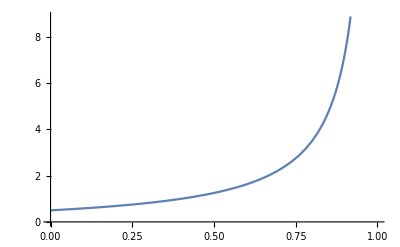

```mathematica
a=0.5;
R=2;
L=1;
Plot[Vs1 /. V[[1]],{gamma,0,1}]
Plot[Vs2 /. V[[1]],{gamma,0,1}]
```

```mathematica
Clear[a,p1,p2];
a = p1*p2 + (1-p1)*(1-p2);
Vs1 /. V[[1]]

dVp1 = D[Vs1+Vs2 /. V[[1]], p1]
dVp2 = D[Vs1+Vs2 /. V[[1]], p2]
p1=0.9;
p2=0.1;
Plot[Vs1+Vs2/.V[[1]], {gamma,0,1}]

Plot[dVp1 /. V[[1]],{gamma,0,1}]
```

-(L-gamma L+gamma L p1-gamma^2 L p1+gamma^2 L p1^2+gamma^2 R-2 gamma^2 p1 R+gamma^2 p1^2 R)/((-1+gamma) (1-gamma^2 p1+gamma^2 p1^2))

-(gamma L-gamma^2 L+2 gamma^2 L p1-2 gamma^2 R+2 gamma^2 p1 R)/((-1+gamma) (1-gamma^2 p1+gamma^2 p1^2))-(gamma L-gamma^2 L+2 gamma^2 L p1-gamma R-gamma^2 R+2 gamma^2 p1 R)/((-1+gamma) (1-gamma^2 p1+gamma^2 p1^2))+((-gamma^2+2 gamma^2 p1) (L-gamma L+gamma L p1-gamma^2 L p1+gamma^2 L p1^2+gamma^2 R-2 gamma^2 p1 R+gamma^2 p1^2 R))/((-1+gamma) (1-gamma^2 p1+gamma^2 p1^2)^2)+((-gamma^2+2 gamma^2 p1) (gamma L p1-gamma^2 L p1+gamma^2 L p1^2+gamma R-gamma p1 R-gamma^2 p1 R+gamma^2 p1^2 R))/((-1+gamma) (1-gamma^2 p1+gamma^2 p1^2)^2)

0

-Graphics-

-Graphics-

```mathematica
(* 1P 3-state MDP *)
```

```mathematica
Clear[Vs1,Vs2,Vs3,V,p1,R,L,gamma];
Rmat = {L,0,R};
Pmat = {{p1,1-p1,0},{p1,0,1-p1},{0,p1,1-p1}};
p0 = {1,0,0};
V = p0.Inverse[IdentityMatrix[3]-gamma*Pmat].Rmat;
FullSimplify[V]
```

(L (-1-gamma (-1+p1) (1+gamma p1))-gamma^2 (-1+p1)^2 R)/((-1+gamma) (1+gamma^2 (-1+p1) p1))

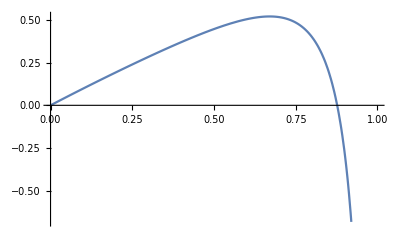

{gamma→0.87678}

```mathematica
Clear[p1,L,R,gamma];
dVp1 = D[V, p1];
L=1; (* Communism *)
R=2; (* Fascism *)
p1=0.7; (* Probability of getting blue pilled *)
Plot[dVp1,{gamma,0,1}]
FindRoot[dVp1,{gamma,0.8}]
```

```mathematica
(* Recursion ---------------------------------*)
Clear[Vs1,Vs2,Vs3,V,p1,R,L,gamma];
(* s1 = left (lower reward) *)
(* s2 = moderate (no reward) *)
(* s3 = right (higher reward) *)
V =Solve[{Vs1 ==L + p1*gamma*Vs1 + (1-p1)*gamma*Vs2, Vs2 == p1*gamma*Vs1 + (1-p1)*gamma*Vs3, Vs3==R+p1*gamma*Vs2+(1-p1)*gamma*Vs3},{Vs1,Vs2,Vs3}];
p1=0
FullSimplify[V]
Series[Vs3/.V[[1]],{gamma,0,2}]
```

0

{{Vs1→L-(gamma^2 R)/(-1+gamma),Vs2→-(gamma R)/(-1+gamma),Vs3→-R/(-1+gamma)}}

R+R gamma+R gamma^2+O[gamma]^3

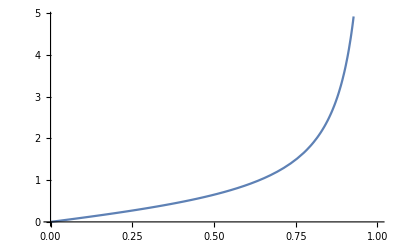

{gamma→5.01103×10^-17}

```mathematica
Clear[p1,L,R,gamma];
dVp1 = D[Vs1/. V[[1]], p1];
L=1; (* Communism *)
R=2; (* Fascism *)
p1=0.8; (* Probability of getting blue pilled *)
Plot[dVp1 /. V[[1]],{gamma,0,1}]
FindRoot[dVp1,{gamma,0.8}]
```

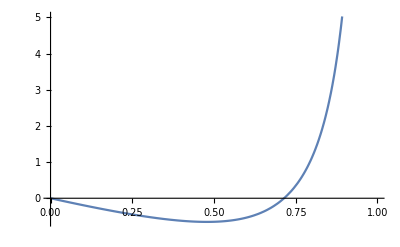

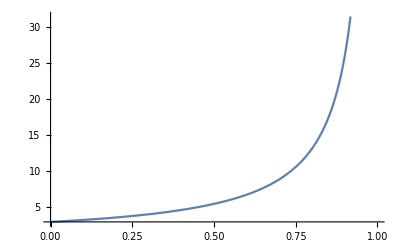

(0.6 gamma^2 (1.2 gamma-0.48 gamma^2))/((-1+gamma) (1-0.16 gamma^2)^2)-(gamma-0.2 gamma^2)/((-1+gamma) (1-0.16 gamma^2))+(0.6 gamma^2 (1-0.2 gamma-0.08 gamma^2))/((-1+gamma) (1-0.16 gamma^2)^2)+(0.6 gamma^2 (2-1.6 gamma+0.32 gamma^2))/((-1+gamma) (1-0.16 gamma^2)^2)-(-gamma+1.8 gamma^2)/((-1+gamma) (1-0.16 gamma^2))-(-2 gamma+2.8 gamma^2)/((-1+gamma) (1-0.16 gamma^2))

-(1.2 gamma-0.48 gamma^2)/((-1+gamma) (1-0.16 gamma^2))-(1-0.2 gamma-0.08 gamma^2)/((-1+gamma) (1-0.16 gamma^2))-(2-1.6 gamma+0.32 gamma^2)/((-1+gamma) (1-0.16 gamma^2))

```mathematica
Plot[dVp1,{gamma,0,1}]
Plot[Vs1+Vs2+Vs3 /. V[[1]], {gamma,0,1}]
dVp1
Vs1+Vs2+Vs3 /. V[[1]]
```

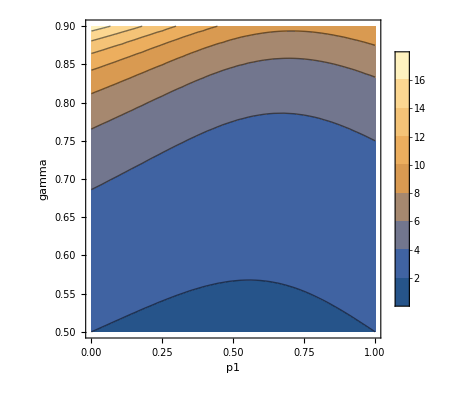

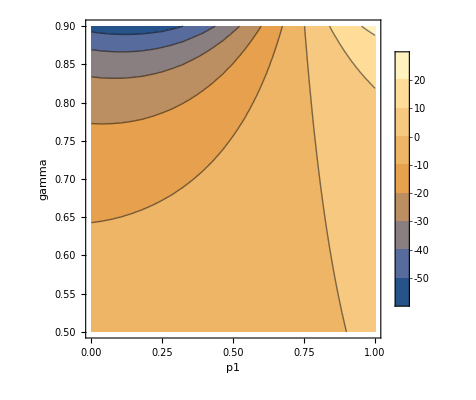

```mathematica
Clear[p1,gamma];
ContourPlot[Vs1 /. V[[1]],{p1,0,1},{gamma,0.5,0.9},AxesLabel->{p1,gamma},PlotRange->Full,PlotLegends->Automatic]
ContourPlot[dVp1,{p1,0,1},{gamma,0.5,0.9},AxesLabel->{p1,gamma},PlotLegends->Automatic]
```

```mathematica
(* 1P 3-state MDP with initial conditions *)
Clear[Vs0,Vs1,Vs2,Vs3,V,p1,R,L,gamma];
(* s1 = left (lower reward) *)
(* s2 = moderate (no reward) *)
(* s3 = right (higher reward) *)
V =Solve[{Vs1 ==L + p1*gamma*Vs1 + (1-p1)*gamma*Vs2, Vs2 == p1*gamma*Vs1 + (1-p1)*gamma*Vs3, Vs3==R+p1*gamma*Vs2+(1-p1)*gamma*Vs3},{Vs1,Vs2,Vs3}];
FullSimplify[V]
Series[Vs3/.V[[1]],{gamma,0,2}]
```